```mathematica
μ:= (1-β^2/3-λ)+ⅈ β/(√3)(1-λ)
```

```mathematica
μ2 :=(1-λ) + ⅈ β/(√3)
μ3:= (1-β^2/6- λ) - β/6 √(β^2-12(1-λ))
```

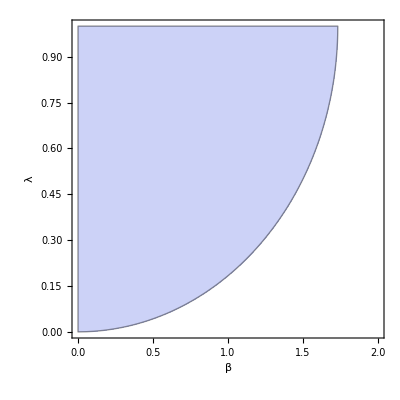

```mathematica
RegionPlot[Abs[μ2] < 1,  {β,0, 2}, {λ, 0, 1}, FrameLabel->{β,λ}]
```

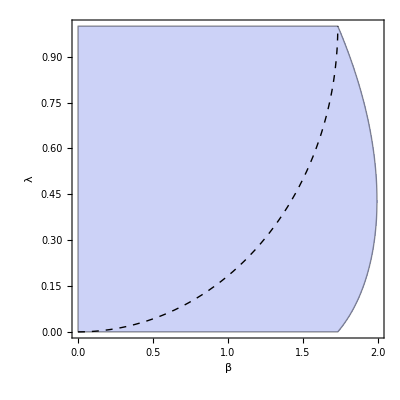

```mathematica
Show[RegionPlot[Abs[μ] < 1, {β,0, 2}, {λ, 0, 1}], ContourPlot[Abs[μ2],  {β,0, 2}, {λ, 0, 1}, Contours->{1}, ContourShading->None, ContourStyle-> Dashed],FrameLabel->{β,λ}]
```

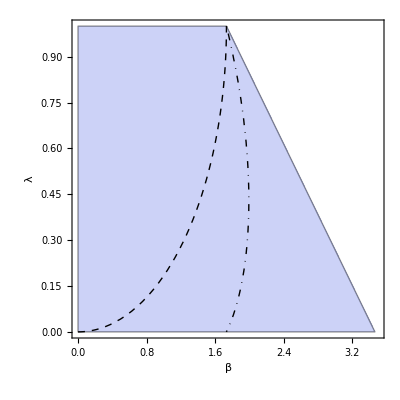

```mathematica
Show[RegionPlot[Abs[μ3] < 1, {β,0, 3.5}, {λ, 0, 1}], ContourPlot[Abs[μ2],  {β,0, 3.5}, {λ, 0, 1}, Contours->{1}, ContourShading->None, ContourStyle-> Dashed],ContourPlot[Abs[μ],  {β,0, 3.5}, {λ, 0, 1}, Contours->{1}, ContourShading->None, ContourStyle->DotDashed],FrameLabel->{β,λ}]
```

```mathematica
Export["D:\\Users\\User\\Dropbox\\Dropbox\\MPhys Project\\kLR notes files\\k2k2stability.png", %13, ImageResolution-> 300]
```

D:\Users\User\Dropbox\Dropbox\MPhys Project\kLR notes files\k2k2stability.png

```mathematica
Export["D:\\Users\\User\\Dropbox\\Dropbox\\MPhys Project\\kLR notes files\\k1k1stability.png", %14, ImageResolution-> 300]
```

D:\Users\User\Dropbox\Dropbox\MPhys Project\kLR notes files\k1k1stability.png

```mathematica
Export["D:\\Users\\User\\Dropbox\\Dropbox\\MPhys Project\\kLR notes files\\k2k1stability.png", %23, ImageResolution-> 300]
```

D:\Users\User\Dropbox\Dropbox\MPhys Project\kLR notes files\k2k1stability.png

```mathematica
datak1k2variance := Import["D:\\Users\\User\\Dropbox\\Dropbox\\MPhys Project\\cpp\\k-level reasoning in large games - good version 21-03\\k1 vs k2\\alice_variance0.dat"]
datak2k1variance := Import["D:\\Users\\User\\Dropbox\\Dropbox\\MPhys Project\\cpp\\k-level reasoning in large games - good version 21-03\\k2 vs k1\\alice_variance0.dat"]
datak2k2variance :=Import["D:\\Users\\User\\Dropbox\\Dropbox\\MPhys Project\\cpp\\k-level reasoning in large games - work in progress\\k2 vs k2\\alice_variance0 b1.6-3.1.dat"]
```

```mathematica
ListDensityPlot[datak2k1variance, InterpolationOrder -> 0, PlotRange->{All,All, Automatic}, ColorFunction-> "SunsetColors", PlotLegends->Automatic]
```

```mathematica
Show[%29, ContourPlot[Abs[μ3],  {β,0, 3.5}, {λ, 0, 1}, Contours->{1}, ContourShading->None, ContourStyle-> {Gray,Dashed}], FrameLabel->{β,λ}]
```

-Graphics-

```mathematica
Show[ListDensityPlot[datak2k2variance, InterpolationOrder -> 0, PlotRange->{All,All, Automatic}, ColorFunction-> "SunsetColors", PlotLegends->Automatic], ContourPlot[Abs[μ],  {β,0, 3}, {λ, 0, 1}, Contours->{1}, ContourShading->None, ContourStyle-> {Gray,Dashed}], FrameLabel->{β,λ}]
```

-Graphics-

```mathematica
Export["D:\\Users\\User\\Dropbox\\Dropbox\\MPhys Project\\kLR notes files\\k2k2variance.png", Rasterize[%49], ImageResolution-> 300]
```

D:\Users\User\Dropbox\Dropbox\MPhys Project\kLR notes files\k2k2variance.png

```mathematica
Export["D:\\Users\\User\\Dropbox\\Dropbox\\MPhys Project\\kLR notes files\\k2k1variance.png", Rasterize[%50], ImageResolution-> 300]
```

D:\Users\User\Dropbox\Dropbox\MPhys Project\kLR notes files\k2k1variance.png